```mathematica
inputFile=NotebookDirectory[]<>"data/hardware_large_square.csv";
inputTable=Import@inputFile;
Xs=#[[5]]&/@inputTable[[2;;]];
Ys=#[[6]]&/@inputTable[[2;;]];

lineMap={#[[1;;2]],#[[3;;4]]}&/@Import[NotebookDirectory[]<>"data/extended_map.csv"];
lineMapSmall={#[[1;;2]],#[[3;;4]]}&/@Import[NotebookDirectory[]<>"data/map.csv"];
```

```mathematica
plotRange={{Min@Xs,Max@Xs},{Min@Ys,Max@Ys}}+{{-1,1},{-1,1}};
```

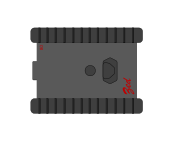
```mathematica
zed=-Graphics-;
```

```mathematica
Manipulate[
GraphicsGrid[Transpose@{
{Graphics[{
{Transparent,EdgeForm@Black,
Rotate[
Translate[
Scale[Inset[zed,{0,0}],1.8/(Differences@plotRange[[1]])//First ],
inputTable[[x]][[5;;6]]
],
inputTable[[x]][[7]]
]
},
{Thick,Black,Line[lineMap]},
{Darker@Red,Circle[inputTable[[x]][[5;;6]],2*inputTable[[x]][[8;;9]]]}
},
PlotRange->plotRange
]},
{ListPlot[Transpose[{(#[[1]]&/@inputTable),Norm/@(#[[8;;9]]&/@inputTable)}],Joined->True,GridLines->{{{(#[[1]]&/@inputTable)[[x]],Red}},None}]}
},
ImageSize->800
],
{x,2,Length@inputTable,1,AnimationRate->10}
]
```